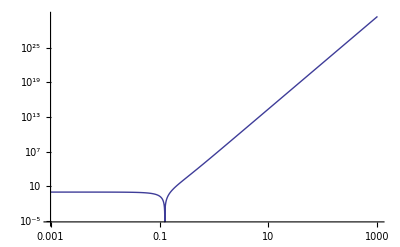

```mathematica
PSD[f_,sigma_,b1_,b2_,b3_,b4_]:=sigma^2*(b1*(2*π*ⅈ*f)^4+b2*(2*π*ⅈ*f)^3+b3*(2*π*ⅈ*f)^2+b4*(2*π*ⅈ*f)+1)*(b1*(-2*π*ⅈ*f)^4+b2*(-2*π*ⅈ*f)^3+b3*(-2*π*ⅈ*f)^2+b4*(-2*π*ⅈ*f)+1);
LogLogPlot[PSD[f,1,-1,0,1,0],{f,0.001,1000}]
```